```mathematica
Quit
```

# Find All Diagrams

Generate all forward and conjugate diagrams and report their counts.

## Load Card

```mathematica
CardName="UU"
```

UU

## Initialization

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Addon","Load","LoadFACET.wl"}]];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynCalcLegacy 1.0.0

FeynCalcLegacy contains legacy functions and symbols that were removed in FeynCalc 10.2.1

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynFacet 0.1

## Setup

```mathematica
Setup=Get[FileNameJoin[{NotebookDirectory[],"Cards",CardName<>".wl"}]];
```

## Diagram Generation

```mathematica
DiagramsBySide=GenerateDiagram[Setup];
```

## Foward Diagrams

Forward diagrams

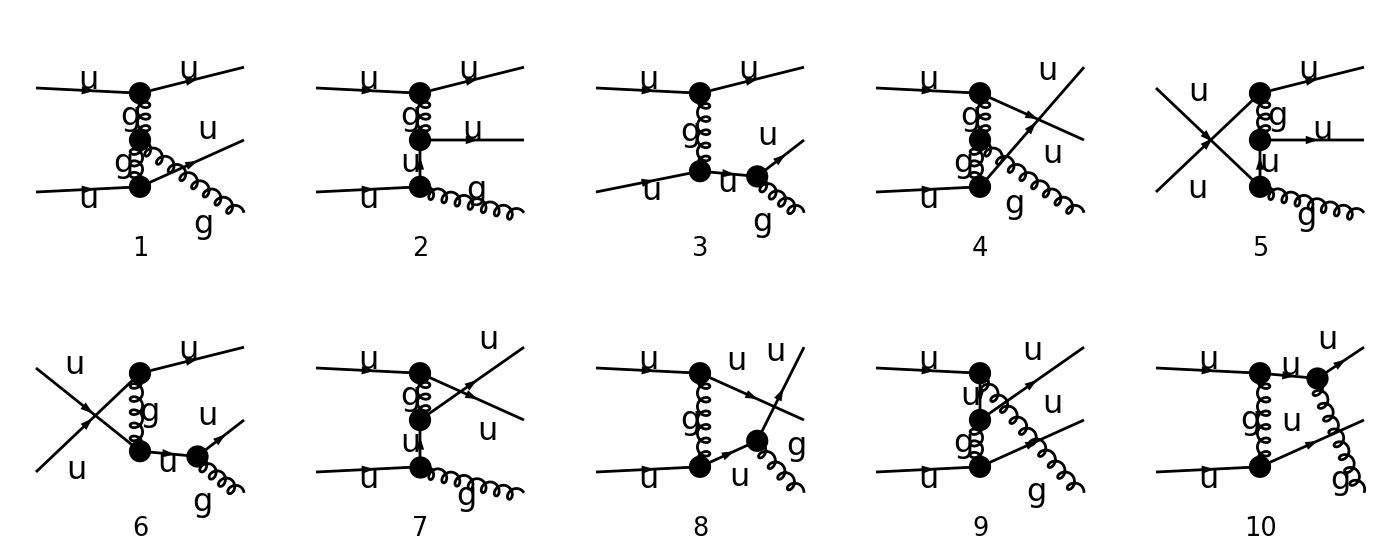

```mathematica
Print["Forward diagrams"];Scan[Print,Render[Paint[DiagramsBySide["Amplitude"],ColumnsXRows->{5,2},Numbering->Simple,SheetHeader->None,DisplayFunction->Identity],ImageSize->{1400,560}]];
```

## Conjugate Diagrams

```mathematica
Print["Conjugate diagrams"];Scan[Print,Render[Paint[DiagramsBySide["Conjugate"],ColumnsXRows->{5,2},Numbering->Simple,SheetHeader->None,DisplayFunction->Identity],ImageSize->{1400,560}]];
```

Conjugate diagrams

-Graphics-